```mathematica
Quit
```

# Examples of Multi-Field Vacuum Decay

This tutorial contains examples of false vacuum decay in potential with multiple scalar fields computed with Polygonal Bounces approach.

Loads the package

```mathematica
SetDirectory[FileNameTake[NotebookDirectory[],{1,-4}]];
<<"FindBounce.m"
```

```mathematica
Get["FindBounce`"]
```

## False vacuum decay

## Single Field Potential

### Potential

```mathematica
U1[ϕ_]:=Block[{αs = .9,V},V = 1/2(ϕ)^2-1/2(ϕ)^3+αs/8 (ϕ)^4 ];
Extrema1=Block[{φ},φ/.Sort@NSolve[(D[U1[φ],φ])==0,φ]];
```

### Bounce

```mathematica
PB1 =  FindBounce[ U1,Extrema1[[1]],Extrema1[[3]] ][[1]] ;
```

### Plot

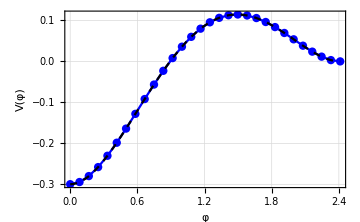
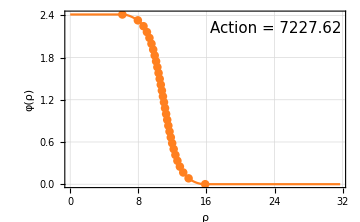

```mathematica
Block[{aRw,ϕN3,a,R,v,b,d,ϕL,VL,dVL,ddVL,α,ℐ,dℐ,r,β,ν,r1,Ns,pos,forBack,timeRw,ϕt,ϕ,Nφ,l,eL,ϕs,vs,as,bs,Rs,Ts,Vs,Tξ,Vξ,T1,V1,Rw,methodRw,maxIteR,accuracyB,ansatzRw,accuracyPath,iteζ,methodSeg,Nfv,aV1,plot,listϕLVL ,listRϕL},
(*======================*)
{aRw,ϕN3,a,R,v,b,d,ϕL,VL,dVL,ddVL,α,ℐ,dℐ,r,β,ν,r1,Ns,pos,forBack,timeRw,ϕt,ϕ,Nφ,l,eL,ϕs,vs,as,bs,Rs,Ts,Vs,Tξ,Vξ,T1,V1,Rw,methodRw,maxIteR,accuracyB,ansatzRw,accuracyPath,iteζ,methodSeg,Nfv,aV1}=PB1;
(*======================*)
listϕLVL = Show[ListPlot[Transpose@{ϕL,VL},PlotStyle->Blue,Joined->True,Frame->True,Mesh->Full, LabelStyle->Directive[Black,FontSize->20, FontFamily->"Times New Roman",FontSlant->Plain],FrameLabel->{"φ","V(φ)"},GridLines->Automatic,ImageSize->Medium],Plot[U1[ϕL[[-1]]-ϕ],{ϕ,0,ϕL[[-1]]},PlotStyle->{Black,Dashed}]];
listRϕL = Show[ 
If[pos==1,Plot[  Sign[ϕ[[-1]]-ϕ[[1]]](  v[[pos]]+ 4/d a[[pos]]R[[pos]]^2 +2/(d-2)b[[pos]]/R[[pos]]^(d-2)-Abs[ϕ[[-1]]-ϕ[[1]]])+ ϕ[[-1]],{ρ,0.,R[[pos]]},PlotStyle->RGBColor[1,0.5,1/8],Axes->False,Epilog->{Text[Style[Row[{"Action = ",T1+V1+Tξ+Vξ}],10,15,"Times New Roman"],Scaled[{0.75,0.9}],Background->LightGreen]} ],Plot[ Sign[ϕ[[-1]]-ϕ[[1]]]( (v[[pos-1]]+ 4/d a[[pos-1]]ρ^2 )-Abs[ϕ[[-1]]-ϕ[[1]]])+ ϕ[[-1]],{ρ,0.,R[[pos]]},PlotStyle->RGBColor[1,0.5,1/8],Axes->False]],
(*====================*)
Table[Plot[{  Sign[ϕ[[-1]]-ϕ[[1]]]( ( v[[s]] + 4/d a[[s]]ρ^2 +If[ρ>0,2/(d-2)b[[s]]/ρ^(d-2),0] ) -Abs[ϕ[[1]]])+ Abs[ϕ[[-1]]] },{ρ,R[[s]],R[[s+1]]},PlotStyle->RGBColor[1,0.5,1/8]],{s,pos,Ns}]
(*====================*)
,Plot[{  Sign[ϕ[[-1]]-ϕ[[1]]](( v[[Ns]] + 4/d a[[Ns]]R[[-1]]^2 +2/(d-2)b[[Ns]]/R[[-1]]^(d-2) ) -Abs[ϕ[[1]]])+ Abs[ϕ[[-1]]]   },{ρ,R[[-1]],R[[-1]]2},PlotStyle->RGBColor[1,0.5,1/8]]
(*====================*)
,ListPlot[{R,ϕ}//Transpose,PlotStyle->{RGBColor[1,0.5,1/8],PointSize[.017]}]
,Frame->True,
FrameLabel->{"ρ","φ(ρ)"},LabelStyle->Directive[Black,FontSize->17, FontFamily->"Times New Roman",FontSlant->Plain],GridLines->Automatic ,GridLinesStyle->GrayLevel[.85],ImageSize->Medium,PlotRange->All ] ;
plot1 = {listϕLVL,listRϕL};
Row[{listϕLVL,listRϕL}]  ]
```

### -Options

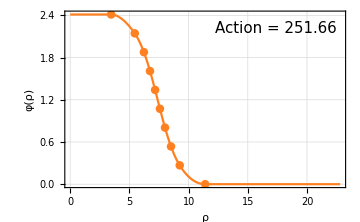

```mathematica
(*Options[FindBounce]//MatrixForm*)
(*Derivative of V*)
dU1[ϕ_]:=Block[{αs=.9,V},V= ϕ-(3 ϕ^2)/2+(αs ϕ^3)/2];
(*Bounce*)
PB1 =  FindBounce[ U1,Extrema1[[1]],Extrema1[[3]],  "NumberSegments"->9, "Dimension"->3,derivativeV-> dU1,"AccuracyBounce"->4,"AnsatzRadii"->10  ][[1]] ;
(*Plot*)
Block[{aRw,ϕN3,a,R,v,b,d,ϕL,VL,dVL,ddVL,α,ℐ,dℐ,r,β,ν,r1,Ns,pos,forBack,timeRw,ϕt,ϕ,Nφ,l,eL,ϕs,vs,as,bs,Rs,Ts,Vs,Tξ,Vξ,T1,V1,Rw,methodRw,maxIteR,accuracyB,ansatzRw,accuracyPath,iteζ,methodSeg,Nfv,aV1},
(*======================*)
{aRw,ϕN3,a,R,v,b,d,ϕL,VL,dVL,ddVL,α,ℐ,dℐ,r,β,ν,r1,Ns,pos,forBack,timeRw,ϕt,ϕ,Nφ,l,eL,ϕs,vs,as,bs,Rs,Ts,Vs,Tξ,Vξ,T1,V1,Rw,methodRw,maxIteR,accuracyB,ansatzRw,accuracyPath,iteζ,methodSeg,Nfv,aV1}=PB1;
(*======================*)
Show[ 
If[pos==1,Plot[  Sign[ϕ[[-1]]-ϕ[[1]]](  v[[pos]]+ 4/d a[[pos]]R[[pos]]^2 +2/(d-2)b[[pos]]/R[[pos]]^(d-2)-Abs[ϕ[[-1]]-ϕ[[1]]])+ ϕ[[-1]],{ρ,0.,R[[pos]]},PlotStyle->RGBColor[1,0.5,1/8],Axes->False,Epilog->{Text[Style[Row[{"Action = ",T1+V1+Tξ+Vξ}],10,15,"Times New Roman"],Scaled[{0.75,0.9}],Background->LightGreen]} ],Plot[ Sign[ϕ[[-1]]-ϕ[[1]]]( (v[[pos-1]]+ 4/d a[[pos-1]]ρ^2 )-Abs[ϕ[[-1]]-ϕ[[1]]])+ ϕ[[-1]],{ρ,0.,R[[pos]]},PlotStyle->RGBColor[1,0.5,1/8],Axes->False]],
(*====================*)
Table[Plot[{  Sign[ϕ[[-1]]-ϕ[[1]]]( ( v[[s]] + 4/d a[[s]]ρ^2 +If[ρ>0,2/(d-2)b[[s]]/ρ^(d-2),0] ) -Abs[ϕ[[1]]])+ Abs[ϕ[[-1]]] },{ρ,R[[s]],R[[s+1]]},PlotStyle->RGBColor[1,0.5,1/8]],{s,pos,Ns}]
(*====================*)
,Plot[{  Sign[ϕ[[-1]]-ϕ[[1]]](( v[[Ns]] + 4/d a[[Ns]]R[[-1]]^2 +2/(d-2)b[[Ns]]/R[[-1]]^(d-2) ) -Abs[ϕ[[1]]])+ Abs[ϕ[[-1]]]   },{ρ,R[[-1]],R[[-1]]2},PlotStyle->RGBColor[1,0.5,1/8]]
(*====================*)
,ListPlot[{R,ϕ}//Transpose,PlotStyle->{RGBColor[1,0.5,1/8],PointSize[.017]}]
,Frame->True,
FrameLabel->{"ρ","φ(ρ)"},LabelStyle->Directive[Black,FontSize->17, FontFamily->"Times New Roman",FontSlant->Plain],GridLines->Automatic ,GridLinesStyle->GrayLevel[.85],ImageSize->Medium,PlotRange->All ] ]
```

## >Two Field Potential

### Potential

```mathematica
caseB =True; (*Type B potential*)
If[caseB,
(*Case B*)
	μλαϵ={{80.,100.},{.1,.3},2.,{0.,0.}} ;
	rangeU={-16000,1000};
	Extrema2 = {{0,12.9099},{6.25901,6.00687},{20.,0.}};,
(*Case A*)
	μλαϵ= {{80.,100.},{.1,.3},2.,{0.,800.}}; 
	rangeU={-20000,5000};
	Extrema2 = {{0,10.},{2.51278,6.27444},{19.9167,-0.576745}};];
Potential2[ϕ_]:=Sum[-μλαϵ[[1,i]] (ϕ[[i]])^2 +μλαϵ[[2,i]](ϕ[[i]])^4+μλαϵ[[4,i]]ϕ[[i]] ,{i,1,2}]+ μλαϵ[[3]](ϕ[[1]])^2 (ϕ[[2]])^2;
```

### Bounce

```mathematica
Block[{time},
{time,PB2} =FindBounce[Potential2,Extrema2[[1]],Extrema2[[3]],"InitialFieldValue"->Extrema2[[2]]]//AbsoluteTiming;

(*==========================*)
Column[{Row[{"Total time consumed = ",time," s."}],
MatrixForm[Join[{{"ite","Bounce","Path"}},Transpose@Join[{Table[ToString[i],{i,Length[PB2]}]},Transpose@PB2[[All,22;;23]]]],TableHeadings->{None,{"","Time(s)"}}]  }]     ]
```

Total time consumed = 0.180139 s.
( | Time(s) | 
ite | Bounce | Path
1 | 0.026088 | 0
2 | 0.01669 | 0.021959
3 | 0.009277 | 0.022104
4 | 0.009108 | 0.023007)

### Plot

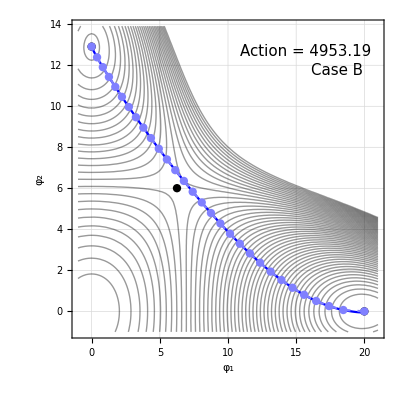
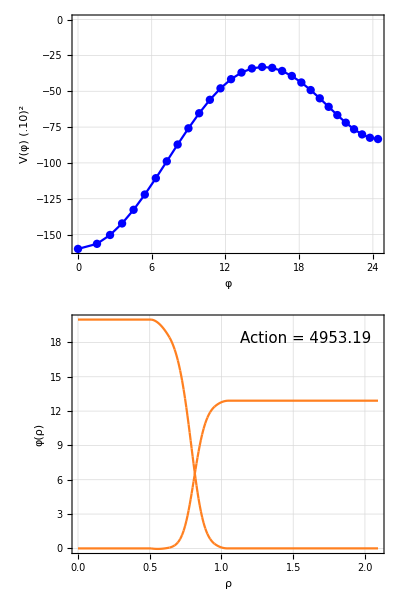

```mathematica
Block[{aRw,ϕN3,a,R,v,b,d,ϕL,VL,dVL,ddVL,α,ℐ,dℐ,r,β,ν,r1,Ns,pos,forBack,timeRw,ϕt,ϕ,Nφ,l,eL,ϕs,vs,as,bs,Rs,Ts,Vs,Tξ,Vξ,T1,V1,Rw,methodRw,maxIteR,accuracyB,ansatzRw,accuracyPath,iteζ,methodSeg,Nfv,aV1,imagesize,fontsize,surf,ko,contourV,extremaV,ps,MMPBPath,Φ1,Φ2,Φ3,i,listϕLVL,listRϕL},
(*======================*)
{aRw,ϕN3,a,R,v,b,d,ϕL,VL,dVL,ddVL,α,ℐ,dℐ,r,β,ν,r1,Ns,pos,forBack,timeRw,ϕt,ϕ,Nφ,l,eL,ϕs,vs,as,bs,Rs,Ts,Vs,Tξ,Vξ,T1,V1,Rw,methodRw,maxIteR,accuracyB,ansatzRw,accuracyPath,iteζ,methodSeg,Nfv,aV1}  = PB2[[-1]];
(*======================*)
imagesize = 400;fontsize =20;
contourV = ContourPlot[ Potential2[{ϕ1,ϕ2}],{ϕ1,-1,21},{ϕ2,If[caseB,-1,-1.2],Extrema2[[1,2]]+1},PlotRange->rangeU,ContourShading->None,GridLines->Automatic,Contours->50,GridLinesStyle->Directive[Dashed,GrayLevel[.85]],ContourStyle->Opacity[0.4],FrameLabel->{"φ_1","φ_2"},ImageSize->imagesize,LabelStyle->Directive[Black,FontSize->25, FontFamily->"Times New Roman",FontSlant->Plain],Epilog->{{Text[Style[Row[{"Action = ",T1+V1+Tξ+Vξ}],10,15,"Times New Roman"],Scaled[{0.75,0.9}],Background->LightGreen]},{Text[Style[If[caseB,"Case B","Case A"],10,15,"Times New Roman"],Scaled[{0.85,0.84}],Background->LightRed]}} ];
extremaV =ListPlot[ Extrema2 ,PlotStyle->{PointSize[.015],Black} ];
ps = If[pos>1,pos-1,pos];i=-1;
MMPBPath =  { Table[  ParametricPlot[
vs[[i,s]]+4/d as[[i,s]]ρ^2+If[pos>1&&s==ps,0.,2/(d-2)bs[[i,s]]/ρ^(d-2)],{ρ,Min[Rs[[i,s]]],Min[Rs[[i,s+1]]]},PlotStyle->Blue, LabelStyle->Directive[Black,FontSize->16, FontFamily->"Times New Roman",FontSlant->Plain],AxesLabel->{"φ_1","φ_2"},ImageSize->350,AxesOrigin->{-1,-1}],{s,ps,Ns}],ListPlot[    If[ pos>1,Join[{vs[[i,pos-1]]},ϕs[[i,pos;;-1]]],ϕs[[i]]]  ,PlotStyle->{Lighter[Blue,.5],Dashed,If[i<iteζ+1,Dashed]},Joined->True,Mesh->All]} ;
listϕLVL = ListPlot[Transpose@{ϕL,VL/100},PlotStyle->Blue,Joined->True,Frame->True,Mesh->Full, LabelStyle->Directive[Black,FontSize->20, FontFamily->"Times New Roman",FontSlant->Plain],FrameLabel->{"φ","V(φ) (.10)^2"},GridLines->Automatic,ImageSize->Medium];
listRϕL = Show[ 
If[pos==1,Plot[  vs[[i,pos]]+ 4/d as[[i,pos]]R[[pos]]^2 +2/(d-2)bs[[i,pos]]/R[[pos]]^(d-2),{ρ,0.,R[[pos]]},PlotStyle->RGBColor[1,0.5,1/8],Axes->False,Epilog->{Text[Style[Row[{"Action = ",T1+V1+Tξ+Vξ}],10,15,"Times New Roman"],Scaled[{0.75,0.9}],Background->LightGreen]} ],Plot[(vs[[i,pos-1]]+ 4/d as[[i,pos-1]]ρ^2 ),{ρ,0.,R[[pos]]},PlotStyle->RGBColor[1,0.5,1/8],Axes->False,Epilog->{Text[Style[Row[{"Action = ",T1+V1+Tξ+Vξ}],10,15,"Times New Roman"],Scaled[{0.75,0.9}],Background->LightGreen]} ]],
(*====================*)
Table[Plot[( vs[[i,s]] + 4/d as[[i,s]]ρ^2 +If[ρ>0,2/(d-2)bs[[i,s]]/ρ^(d-2),0] ),{ρ,R[[s]],R[[s+1]]},PlotStyle->RGBColor[1,0.5,1/8]],{s,pos,Ns}]
(*====================*)
,Plot[( vs[[i,Ns]] + 4/d as[[i,Ns]]Rs[[i,-1]]^2 +2/(d-2)bs[[i,Ns]]/Rs[[i,-1]]^(d-2) ),{ρ,R[[-1]],R[[-1]]2},PlotStyle->RGBColor[1,0.5,1/8]]
(*====================*)
,Frame->True,
FrameLabel->{"ρ","φ(ρ)"},LabelStyle->Directive[Black,FontSize->17, FontFamily->"Times New Roman",FontSlant->Plain],GridLines->Automatic ,GridLinesStyle->GrayLevel[.85],ImageSize->Medium,PlotRange->All ] ;
plot2 = {Show[contourV,extremaV,Show[MMPBPath ],PlotRange->All,ImageSize->imagesize],Column[{listϕLVL ,listRϕL }]};
Row[{Show[contourV,extremaV,Show[MMPBPath ],PlotRange->All,ImageSize->imagesize],Column[{listϕLVL ,listRϕL }]}]  ]
```

## >Three Field Potential

### The Potential

```mathematica
{typeV,Extrema3,parameters3}=Block[{μ1=40,μ2=100,μ3=120,λ1=.1,λ2=.2,λ3=.3,α1=2,α2=2.1,α3=1.2,ϵ1 =100,ϵ2 = 150,ϵ3 = 100,V,Φ,ϕ1,ϕ2,ϕ3,dV,d2V,sols,typeV,Extrema,ExtremaAnsatz,singEig ,parameters3},
V[ϕ_] := -μ1 (ϕ[[1]])^2-μ2 (ϕ[[2]])^2-μ3 (ϕ[[3]])^2 +λ1 (ϕ[[1]])^4+λ2 (ϕ[[2]])^4+λ3 (ϕ[[3]])^4+ α1 (ϕ[[1]])^2 (ϕ[[2]])^2+α2 (ϕ[[1]])^2 (ϕ[[3]])^2+α3 (ϕ[[2]])^2 (ϕ[[3]])^2 +ϵ1 ϕ[[1]] +ϵ2 ϕ[[2]] +ϵ3 ϕ[[3]] ;
Φ = {ϕ1,ϕ2,ϕ3};
dV = D[V[Φ],{Φ}];
d2V = D[V[Φ],{Φ},{Φ}];
ExtremaAnsatz={{0.,-15.8113883,0.},{6.54653671,-5.976143,0.},{20.,0.,0.}};
(*Find new minima*)
sols = Table[FindRoot[dV,Transpose@{Φ,ExtremaAnsatz[[i]]}],{i,1,3}];
d2V = D[V[Φ],{Φ},{Φ}]/.sols;
singEig =Table[DeleteDuplicates@Sign[Eigenvalues@d2V[[i]]],{i,1,3}];
(*Classify type of minima*)
typeV = Table[If[Length@singEig[[i]] >1,"Saddle",If[singEig[[i,1]] >0,"Minimum","Maximum"]],{i,1,3}];
Extrema = Φ/.sols;
parameters3 = {μ1,μ2,μ3,λ1,λ2,λ3,α1,α2,α3,ϵ1,ϵ2,ϵ3} ;
{typeV,Extrema,parameters3}//Chop
];
Row[{"type of Minima: ",typeV}]
(*=====================*)
Potential3[ϕ_]:=Block[{V,μ1,μ2,μ3,λ1,λ2,λ3,α1,α2,α3,ϵ1,ϵ2,ϵ3},
{μ1,μ2,μ3,λ1,λ2,λ3,α1,α2,α3,ϵ1,ϵ2,ϵ3}=parameters3;
V = -μ1 (ϕ[[1]])^2-μ2 (ϕ[[2]])^2-μ3 (ϕ[[3]])^2 +λ1 (ϕ[[1]])^4+λ2 (ϕ[[2]])^4+λ3 (ϕ[[3]])^4+ α1 (ϕ[[1]])^2 (ϕ[[2]])^2+α2 (ϕ[[1]])^2 (ϕ[[3]])^2+α3 (ϕ[[2]])^2 (ϕ[[3]])^2 +ϵ1 ϕ[[1]] +ϵ2 ϕ[[2]] +ϵ3 ϕ[[3]] ];
```

type of Minima: {Minimum,Saddle,Minimum}

### Bounce

```mathematica
Block[{time},
{time,PB3} =FindBounce[Potential3,Extrema3[[1]],Extrema3[[3]],"InitialFieldValue"->Extrema3[[2]]]//AbsoluteTiming;

(*==========================*)
Column[{Row[{"Total time consumed = ",time," s."}],
MatrixForm[Join[{{"ite","Bounce","Path"}},Transpose@Join[{Table[ToString[i],{i,Length[PB3]}]},Transpose@PB3[[All,22;;23]]]],TableHeadings->{None,{"","Time(s)"}}]  }]     ]
```

Total time consumed = 0.1491 s.
( | Time(s) | 
ite | Bounce | Path
1 | 0.002515 | 0
2 | 0.003421 | 0.026081
3 | 0.003393 | 0.027585
4 | 0.002925 | 0.026668)

### Plot

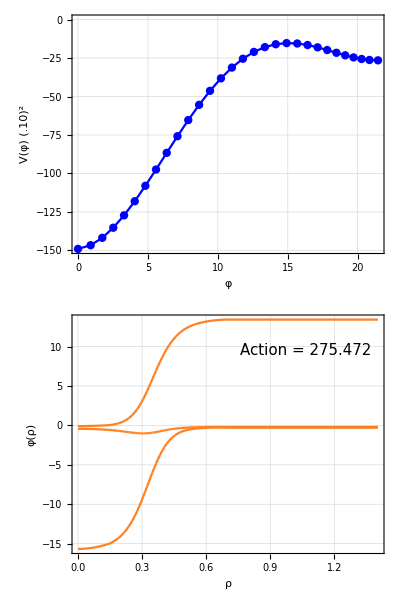
-Graphics3D--Graphics-

```mathematica
Block[{aRw,ϕN3,a,R,v,b,d,ϕL,VL,dVL,ddVL,α,ℐ,dℐ,r,β,ν,r1,Ns,pos,forBack,timeRw,ϕt,ϕ,Nφ,l,eL,ϕs,vs,as,bs,Rs,Ts,Vs,Tξ,Vξ,T1,V1,Rw,methodRw,maxIteR,accuracyB,ansatzRw,accuracyPath,iteζ,methodSeg,Nfv,aV1,imagesize,fontsize,surf,contourV,extremaV,ps,PBPath,Φ1,Φ2,Φ3,i,triangleV,listϕLVL,listRϕL ,z,zPBPath,plotZ,contourZ,potential3,levelZ},
(*======================*)
{aRw,ϕN3,a,R,v,b,d,ϕL,VL,dVL,ddVL,α,ℐ,dℐ,r,β,ν,r1,Ns,pos,forBack,timeRw,ϕt,ϕ,Nφ,l,eL,ϕs,vs,as,bs,Rs,Ts,Vs,Tξ,Vξ,T1,V1,Rw,methodRw,maxIteR,accuracyB,ansatzRw,accuracyPath,iteζ,methodSeg,Nfv,aV1}  = PB3[[-1]];
(*======================*)
imagesize = 400;fontsize =20;
extremaV=ListPointPlot3D[ Extrema3 ,PlotStyle->{Directive[ Orange,PointSize[.02]]}];
ps = If[pos>1,pos-1,pos];i =-1;
triangleV = Graphics3D[{Darker[Red],Thickness[.005],Line[Extrema3]}];
PBPath =   { Table[  ParametricPlot3D[
vs[[i,s]]+4/d as[[i,s]]ρ^2+If[pos>1&&s==ps,0.,2/(d-2)bs[[i,s]]/ρ^(d-2)],{ρ,Min[Rs[[i,s]]],Min[Rs[[i,s+1]]]},PlotStyle->Blue, LabelStyle->Directive[Black,FontSize->16, FontFamily->"Times New Roman",FontSlant->Plain],AxesLabel->{"φ_1","φ_2"},ImageSize->350,AxesOrigin->{-1,-1}],{s,ps,Ns}],ListPointPlot3D[    If[ pos>1,Join[{vs[[i,pos-1]]},ϕs[[i,pos;;-1]]],ϕs[[i]]]  ,PlotStyle->{Lighter[Blue,.5],Dashed,If[i<iteζ+1,Dashed]}],Graphics3D[{Darker[Cyan],Thickness[.005],Line[If[ pos>1,Join[{vs[[i,pos-1]]},ϕs[[i,pos;;-1]]],ϕs[[i]]]]}]} ;
z = {1,2};
zPBPath =    Table[  ParametricPlot[
vs[[i,s,z]]+4/d as[[i,s,z]]ρ^2+If[pos>1&&s==ps,0.,2/(d-2)bs[[i,s,z]]/ρ^(d-2)],{ρ,Min[Rs[[i,s]]],Min[Rs[[i,s+1]]]},PlotStyle->Cyan, LabelStyle->Directive[Black,FontSize->16, FontFamily->"Times New Roman",FontSlant->Plain],AxesLabel->{"φ_1","φ_2"},ImageSize->350,AxesOrigin->{-1,-1}],{s,ps,Ns}];
plotZ =Show[ContourPlot[Potential3[{Φ1,Φ2,-2.5}],{Φ1,-1.5,22},{Φ2,-22,2},Contours->60,GridLines->Automatic,Axes->False,GridLinesStyle->Directive[Dashed,GrayLevel[.85]],ContourStyle->Opacity[0.4],ImageSize->Medium,PlotRangePadding->0,Frame->False,LabelStyle->Directive[Black,FontSize->25, FontFamily->"Times New Roman",FontSlant->Plain]],ListPlot[Transpose@Transpose[Extrema3][[{1,2}]],PlotStyle->{Directive[ Orange,PointSize[.02]]}],ListPlot[Transpose@Transpose[Extrema3][[{1,2}]],PlotStyle->{Red},Joined->True],zPBPath];
potential3  =Show[RegionPlot3D[Potential3[{Φ1,Φ2,Φ3}]<-1500,{Φ1,-1.5,22},{Φ2,-22,2},{Φ3,-2.8,1},PlotStyle->{Directive[Darker[Orange],Opacity[0.5]],Directive[Lighter[Blue],Opacity[0.5]]},Mesh->None,AxesLabel->{"ϕ_1","ϕ_2","ϕ_3"},LabelStyle->Directive[Black,FontSize->25, FontFamily->"Times New Roman",FontSlant->Plain],PlotRange->All,Lighting->"Neutral",Background->None],
triangleV,extremaV,PBPath];
levelZ=-3.5;
contourZ=Graphics3D[{Texture[plotZ],EdgeForm[],Polygon[{{-1.5,-22,levelZ},{22,-22,levelZ},{22,2,levelZ},{-1.5,2,levelZ}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Lighting->"Neutral"];
listϕLVL = ListPlot[Transpose@{ϕL,VL/100},PlotStyle->Blue,Joined->True,Frame->True,Mesh->Full, LabelStyle->Directive[Black,FontSize->20, FontFamily->"Times New Roman",FontSlant->Plain],FrameLabel->{"φ","V(φ) (.10)^2"},GridLines->Automatic,ImageSize->Medium];
listRϕL = Show[ 
If[pos==1,Plot[  vs[[i,pos]]+ 4/d as[[i,pos]]R[[pos]]^2 +2/(d-2)bs[[i,pos]]/R[[pos]]^(d-2),{ρ,0.,R[[pos]]},PlotStyle->RGBColor[1,0.5,1/8],Axes->False,Epilog->{Text[Style[Row[{"Action = ",T1+V1+Tξ+Vξ}],10,15,"Times New Roman"],Scaled[{0.75,0.9}],Background->LightGreen]} ],Plot[(vs[[i,pos-1]]+ 4/d as[[i,pos-1]]ρ^2 ),{ρ,0.,R[[pos]]},PlotStyle->RGBColor[1,0.5,1/8],Axes->False,Epilog->{Text[Style[Row[{"Action = ",T1+V1+Tξ+Vξ}],10,15,"Times New Roman"],Scaled[{0.75,0.85}],Background->LightGreen]} ]],
(*====================*)
Table[Plot[( vs[[i,s]] + 4/d as[[i,s]]ρ^2 +If[ρ>0,2/(d-2)bs[[i,s]]/ρ^(d-2),0] ),{ρ,R[[s]],R[[s+1]]},PlotStyle->RGBColor[1,0.5,1/8]],{s,pos,Ns}]
(*====================*)
,Plot[( vs[[i,Ns]] + 4/d as[[i,Ns]]Rs[[i,-1]]^2 +2/(d-2)bs[[i,Ns]]/Rs[[i,-1]]^(d-2) ),{ρ,R[[-1]],R[[-1]]2},PlotStyle->RGBColor[1,0.5,1/8]]
(*====================*)
,Frame->True,
FrameLabel->{"ρ","φ(ρ)"},LabelStyle->Directive[Black,FontSize->17, FontFamily->"Times New Roman",FontSlant->Plain],GridLines->Automatic ,GridLinesStyle->GrayLevel[.85],ImageSize->Medium,PlotRange->All ] ;
plot3 ={Show[potential3,contourZ,PlotRange->All,BoxRatios->{1,1,1},ImageSize->imagesize],Column[{listϕLVL ,listRϕL }]};
Row[{Show[potential3,contourZ,PlotRange->All,BoxRatios->{1,1,1},ImageSize->imagesize],Column[{listϕLVL ,listRϕL }]}]]
```

## All Plots

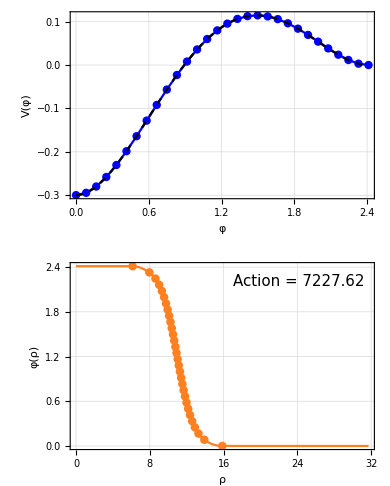
-Graphics--Graphics--Graphics-     -Graphics3D--Graphics-

```mathematica
PLOTS = Magnify[Row[Flatten[{GraphicsGrid[Transpose@{plot1}],plot2,"     ",plot3,"    "}]],.7]
```

```mathematica
(*Export[ FileNameJoin[{FileNameTake[NotebookDirectory[],{1,-5}],"Images","ExaplesBounces.png"}],PLOTS ];*)
```

## Dynamical Examples

## >Single Field Potential

### Sub-Package: bouncePlot

```mathematica
bouncePlot[pts_,d_]:=bouncePlot[pts,d]=
Block[{pos,R,a,v,b,Ts,Vs,φV,Ns,dim,ϕL,VL,dVL,ddVL,α,ℐ,dℐ,r,β,ν,r1,forBack,methodRw,timeRw,ϕt,ϕ,ϕLength,Nφ,l,eL,ϕs,vs,as,bs,Rs,Tξ,Vξ,T1,V1,V=Null,plot,maxIteR,accuracyB,ansatzRw,accuracyPath,iteζ,Rw,aRw,ϕN3,methodSeg,Nfv,aV1},
φV = Transpose[pts];
CheckAbort[{aRw,ϕN3,a,R,v,b,dim,ϕL,VL,dVL,ddVL,α,ℐ,dℐ,r,β,ν,r1,Ns,pos,forBack,timeRw,ϕt,ϕ,Nφ,l,eL,ϕs,vs,as,bs,Rs,Ts,Vs,Tξ,Vξ,T1,V1,Rw,methodRw,maxIteR,accuracyB,ansatzRw,accuracyPath,iteζ,methodSeg,Nfv,aV1}  =FindBounce[V,φV[[1,1]],φV[[1,-1]],"Dimension"->d,"AnsatzPath"->φV[[1]],"AnsatzV1"->φV[[2]]][[1]];
plot =Show[ 
If[pos==1,Plot[  Sign[ϕ[[-1]]-ϕ[[1]]](  v[[pos]]+ 4/d a[[pos]]R[[pos]]^2 +2/(d-2)b[[pos]]/R[[pos]]^(d-2)-Abs[ϕ[[-1]]-ϕ[[1]]])+ ϕ[[-1]],{ρ,0.,R[[pos]]},PlotStyle->RGBColor[1,0.5,1/8],Axes->False],Plot[ Sign[ϕ[[-1]]-ϕ[[1]]]( (v[[pos-1]]+ 4/d a[[pos-1]]ρ^2 )-Abs[ϕ[[-1]]-ϕ[[1]]])+ ϕ[[-1]],{ρ,0.,R[[pos]]},PlotStyle->RGBColor[1,0.5,1/8],Axes->False]],
(*====================*)
Table[Plot[{  Sign[ϕ[[-1]]-ϕ[[1]]]( ( v[[s]] + 4/d a[[s]]ρ^2 +If[ρ>10^-5,2/(d-2)b[[s]]/ρ^(d-2),0] )-Abs[ϕ[[-1]]-ϕ[[1]]])+  ϕ[[-1]]  },{ρ,R[[s]],R[[s+1]]},PlotStyle->RGBColor[1,0.5,1/8],Axes->False],{s,pos,Ns}]
(*====================*)
,Plot[{ Sign[ϕ[[-1]]-ϕ[[1]]]( ( v[[Ns]] + 4/d a[[Ns]]R[[-1]]^2 +2/(d-2)b[[Ns]]/R[[-1]]^(d-2) )-Abs[ϕ[[-1]]-ϕ[[1]]])+ ϕ[[-1]]  },{ρ,R[[-1]],R[[-1]]2},PlotStyle->RGBColor[1,0.5,1/8],Axes->False]
(*====================*)
,ListPlot[Join[If[pos==1,{},{{0, Sign[ϕ[[-1]]-ϕ[[1]]]( v[[pos-1]]-Abs[ϕ[[-1]]-ϕ[[1]]])+ ϕ[[-1]]}}],Transpose[{R[[pos;;-1]], ϕ[[pos;;-1]]}]],PlotStyle->{RGBColor[1,0.5,1/8],PointSize[.017]},Axes->False]
,Frame->True,
FrameLabel->{"ρ","φ(ρ)"},LabelStyle->Directive[Black,FontSize->17, FontFamily->"Times New Roman",FontSlant->Plain],GridLines->Automatic ,GridLinesStyle->GrayLevel[.85],ImageSize->Medium,PlotLabel->Style["Action = "<>ToString[Vs+Ts],Background->LightGreen,FontSize->17],PlotRange->{{0,10},{Min[ϕ],Max[ϕ]}}  ]; ,
plot =ListPlot[{{0,0}},PlotStyle->Red,Epilog->{Inset[Text[Style["$Aborted",Background->LightRed,FontSize->15, FontFamily->"Times New Roman",FontSlant->Plain]],Scaled[{.8,.8}]]}];  ];
Return[plot]];
```

### Plot

```mathematica
DynamicModule[{pts ={{0.,-0.4},{0.15,-0.3},{0.25,0.3},{0.5,0.7},{0.75,0.3},{1,-0}},d=4,ptsT},
ptsT =Transpose[pts];
Row[{LocatorPane[Dynamic[pts],Dynamic[   ListPlot[pts,Joined->True,Mesh->All,PlotRange->{{-0.1,1.1},{Min[ptsT[[2]]] 2,Max[ptsT[[2]]]1.5}},Frame->True,
FrameLabel->{"φ","V(φ)"},GridLines->Automatic,GridLinesStyle->GrayLevel[.85],ImageSize->Medium,MeshStyle->PointSize[Large],LabelStyle->Directive[Black,FontSize->17, FontFamily->"Times New Roman",FontSlant->Plain],PlotStyle->Darker[Blue],Axes->False]      ],Appearance->None],Dynamic[bouncePlot[pts,d]] }]]
```

## >Two Field Potential

### Sub-Package: MbouncePlot

```mathematica
MbouncePlot[μλαϵ_,d_,n_,itePath_,Potential2_,dV_,d2V_,Extrema_]:=Block[{a,R,v,b,dim,ϕL,VL,dVL,ddVL,α,ℐ,dℐ,r,β,ν,r1,Ns,pos,forBack,methodRw,timeRw,ϕt,ϕ,ϕLength,Nφ,l,eL,ϕs,vs,as,bs,Rs,μ,λ,αs,ϵ,ps,MMPBPath,iteζ=1,plot,abort,Ts,Vs,Tξ,Vξ,T1,V1,maxIteR,accuracyB,ansatzRw,accuracyPath,Rw,aRw,ϕN3,methodSeg,Nfv,aV1},
CheckAbort[
abort = False;{aRw,ϕN3,a,R,v,b,dim,ϕL,VL,dVL,ddVL,α,ℐ,dℐ,r,β,ν,r1,Ns,pos,forBack,timeRw,ϕt,ϕ,Nφ,l,eL,ϕs,vs,as,bs,Rs,Ts,Vs,Tξ,Vξ,T1,V1,Rw,methodRw,maxIteR,accuracyB,ansatzRw,accuracyPath,iteζ,methodSeg,Nfv,aV1}=FindBounce[ Potential2,Extrema[[1]],Extrema[[3]],"InitialFieldValue"->Extrema[[2]], "Dimension"->d, "NumerSegments"->n,"MaxIterationsPathDeformation"->itePath ,derivativeV->dV,derivative2V->d2V][[-1]]//Quiet;
ps = If[pos>1,pos-1,pos];
MMPBPath =    { Table[  ParametricPlot[
vs[[iteζ+1,s]]+4/d as[[iteζ+1,s]]ρ^2+If[pos>1&&s==ps,0.,2/(d-2)bs[[iteζ+1,s]]/ρ^(d-2)],{ρ,Min[Rs[[iteζ+1,s]]],Max[Rs[[iteζ+1,s+1]]]},PlotStyle->Green, PlotRange->{{-10,30},{-10,30}}],{s,ps,Ns}],ListPlot[    If[ pos>1,Join[{vs[[iteζ+1,pos-1]]},ϕs[[iteζ+1,pos;;-1]]],ϕs[[iteζ+1]]]  ,PlotStyle->{Lighter[Green,.5],Dashed,If[iteζ+1<iteζ+1,Dashed]},Joined->True,Mesh->All]} ;,
abort =True;
MMPBPath =  ListPlot[Extrema,PlotStyle->Red,Epilog->{Inset[Text[Style["$Aborted",Background->LightRed,FontSize->15, FontFamily->"Times New Roman",FontSlant->Plain]],Scaled[{.8,.8}]]}];      ];
plot = Show[MMPBPath,LabelStyle->Directive[Black,FontSize->20, FontFamily->"Times New Roman",FontSlant->Plain],ImageSize->Medium,Frame->True,
FrameLabel->{"φ_1","φ_2"},AspectRatio->3/4,PlotRange->All];
Return[  {plot,abort,Ts,Vs,Tξ,Vξ,T1,V1,ϕL,VL,R,pos,v,as,vs,bs,Rs,Ns} ];   ];
```

### Plot

```mathematica
DynamicModule[{μ,λ,αs,ϵ,μλαϵ,Extrema,plot,abort,Ts,Vs,Tξ,Vξ,T1,V1,Potential2,dV,d2V,plots,ϕ1,ϕ2,ϕs,ϕL,VL,R,listRϕL,ps,pos,v,listϕLVL,d=4,as,vs,bs,Rs,Ns,i=-1,Extrema0={{0,12.9099},{6.259,6.00687},{20.,0.}}},Manipulate[
 μλαϵ={{μ1,μ2},{λ1,λ2},α,{ϵ1,ϵ2}};
(*========================================*)
Potential2[ϕ_]:=μλαϵ⟦3⟧ ϕ⟦1⟧^2 ϕ⟦2⟧^2-ϕ⟦1⟧^2 μλαϵ⟦1,1⟧-ϕ⟦2⟧^2 μλαϵ⟦1,2⟧+ϕ⟦1⟧^4 μλαϵ⟦2,1⟧+ϕ⟦2⟧^4 μλαϵ⟦2,2⟧+ϕ⟦1⟧ μλαϵ⟦4,1⟧+ϕ⟦2⟧ μλαϵ⟦4,2⟧; 
dV[ϕ_]:= {2 μλαϵ⟦3⟧ ϕ⟦1⟧ ϕ⟦2⟧^2-2 ϕ⟦1⟧ μλαϵ⟦1,1⟧+4 ϕ⟦1⟧^3 μλαϵ⟦2,1⟧+μλαϵ⟦4,1⟧,2 μλαϵ⟦3⟧ ϕ⟦1⟧^2 ϕ⟦2⟧-2 ϕ⟦2⟧ μλαϵ⟦1,2⟧+4 ϕ⟦2⟧^3 μλαϵ⟦2,2⟧+μλαϵ⟦4,2⟧};
d2V[ϕ_]:= {{2 μλαϵ⟦3⟧ ϕ⟦2⟧^2-2 μλαϵ⟦1,1⟧+12 ϕ⟦1⟧^2 μλαϵ⟦2,1⟧,4 μλαϵ⟦3⟧ ϕ⟦1⟧ ϕ⟦2⟧},{4 μλαϵ⟦3⟧ ϕ⟦1⟧ ϕ⟦2⟧,2 μλαϵ⟦3⟧ ϕ⟦1⟧^2-2 μλαϵ⟦1,2⟧+12 ϕ⟦2⟧^2 μλαϵ⟦2,2⟧}};
(*========================================*) 
ϕs ={ϕ1,ϕ2};
Quiet[Extrema = Table[ϕs/.Chop@FindRoot[dV[ϕs],Transpose@{ϕs,Extrema0[[i]]}],{i,3}]//Quiet;
{plot,abort,Ts,Vs,Tξ,Vξ,T1,V1,ϕL,VL,R,pos,v,as,vs,bs,Rs,Ns}= MbouncePlot[μλαϵ,d,n,2,Potential2,dV,d2V,Extrema];
plots[μλαϵ_] :=plots[μλαϵ] =
Show[ ContourPlot[ Potential2[{ϕ1,ϕ2}],{ϕ1,-5,25},{ϕ2,-5,25},PlotRange->{Automatic,5000},GridLines->Automatic,Contours->10,GridLinesStyle->Directive[Dashed,GrayLevel[.85]],ContourStyle->Opacity[0.4],FrameLabel->{"φ_1","φ_2"},LabelStyle->Directive[Black,FontSize->20, FontFamily->"Times New Roman",FontSlant->Plain],PlotPoints->2,MaxRecursion->3] , ListPlot[ Extrema ,PlotStyle->{PointSize[.015],Black} ],plot,Epilog->{{  If[abort,
Text[Style["$Aborted",10,15,"Times New Roman"],Scaled[{0.75,0.9}],Background->LightRed],
 Text[Style[Row[{"Action = ",T1+V1+Tξ+Vξ}],10,15,"Times New Roman"],Scaled[{0.75,0.9}],Background->LightGreen]]}}   ]; 
If[abort,listϕLVL ="$Aborted";listRϕL ="$Aborted";,
listϕLVL = ListPlot[Transpose@{ϕL,VL/100},PlotStyle->Blue,Joined->True,Frame->True,Mesh->Full, LabelStyle->Directive[Black,FontSize->20, FontFamily->"Times New Roman",FontSlant->Plain],FrameLabel->{"φ(ρ)","V(φ) (.10)^2"},GridLines->Automatic,ImageSize->Medium,PlotRange->{{-3,33},{-400,100}}];
listRϕL = ListPlot[Join[If[pos>1,{{0,v[[pos-1]]}},{{0,ϕL[[1]]}}],Transpose@{R[[pos;;-1]],ϕL[[pos;;-1]]},{{10R[[-1]],ϕL[[-1]]}}],PlotStyle->RGBColor[1,0.5,1/8],Joined->True,Frame->True,Mesh->Full, LabelStyle->Directive[Black,FontSize->20, FontFamily->"Times New Roman",FontSlant->Plain],FrameLabel->{"ρ","φ"},GridLines->Automatic,ImageSize->Medium,PlotRange->{{0,5},{-3,33}}];
];];
Row[{Show[plots[μλαϵ],ImageSize->Medium],Column[{listϕLVL ,listRϕL }]}]
,{{μ1,80.,"μ_1"},70,120,Appearance->"Labeled"},{{μ2,100.,"μ_2"},70,120,Appearance->"Labeled"},{{λ1,.1,"λ_1"},.05,.8,Appearance->"Labeled"},{{λ2,.2,"λ_2"},.05,.8,Appearance->"Labeled"},{{α,3.,"α"},0.7,8,Appearance->"Labeled"},{{ϵ1,0.,"ϵ_1"},0,900,Appearance->"Labeled"},{{ϵ2,0.,"ϵ_2"},0,900,Appearance->"Labeled"},{{n,20,"n"},10,30,1,Appearance->"Labeled"},Paneled->False ]]
```